# Notebook for : Advanced Mathematical Methods for Scientists and Engineers I Asymptotic Methods and Perturbation Theory Bender Orzsag

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
December 18, 2020

```mathematica
(* Very much a rough draft - will fix this up later *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink[" Advanced Mathematical Methods for Scientists and Engineers I Asymptotic Methods and Perturbation Theory Bender Orzsag",
"https://www.springer.com/gp/book/9780387989310"]
```

[ Advanced Mathematical Methods for Scientists and Engineers I Asymptotic Methods and Perturbation Theory Bender Orzsag](https://www.springer.com/gp/book/9780387989310)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 806 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Things To Read

```mathematica
(* READ Tutorial:
tutorial/SeriesLimitsAndResidues#9680818
*)
```

```mathematica
(* 
guide/ContinuedFractionsAndRationalApproximations
*)
```

```mathematica
(* READ *) 
?LogicalExpand
```

## Chapter 4

```mathematica
Clear[eq4pt1pt1]
eq4pt1pt1 = {
y'[x] (1 - x y[x] - y[x]^2) ,  (* This does equal zero, but we leave it out *) 
y[0] == 1
};
eq4pt1pt1  // TableForm
```

(1-x y[x]-y[x]^2) y'[x]
y[0]==1

```mathematica
Clear[y4pt1pt2]
y4pt1pt2[n_] := 
y[x]-> Sum[ a[i] x^i , { i , 0 , n } ]
```

```mathematica
Clear[eq4pt1pt2a]
eq4pt1pt2a = 
a[0] == 1
```

a[0]==1

```mathematica
Clear[eq4pt2pt1]
eq4pt2pt1 = {
y'[x] == y[x]^2+ x , 
y[0] == 0 
} ;
eq4pt2pt1 // TableForm
```

y'[x]==x+y[x]^2
y[0]==0

```mathematica
AsymptoticDSolveValue[ eq4pt2pt1  , y[x] ,{x,0,9}]
```

x^2/2+x^5/20+x^8/160

```mathematica
Clear[y4pt2pt2]
y4pt2pt2[n_]:= 
y[x]-> -(1/(x-a)) + Sum[ a[i] (x-a)^i , {i , 0 , n } ]
```

```mathematica
y4pt2pt2[3]
```

y[x]→-1/(-a+x)+a[0]+(-a+x) a[1]+(-a+x)^2 a[2]+(-a+x)^3 a[3]

```mathematica
Collect[ eq4pt1pt1[[1]] /. y4pt2pt2[3] // Expand  , x ] 
eq4pt1pt1[[2]] /. Equal-> Rule
```

y'[x]-y'[x]/(-a+x)^2+(x y'[x])/(-a+x)-x a[0] y'[x]+(2 a[0] y'[x])/(-a+x)-a[0]^2 y'[x]+a x a[1] y'[x]-x^2 a[1] y'[x]-(2 a a[1] y'[x])/(-a+x)+(2 x a[1] y'[x])/(-a+x)+2 a a[0] a[1] y'[x]-2 x a[0] a[1] y'[x]-a^2 a[1]^2 y'[x]+2 a x a[1]^2 y'[x]-x^2 a[1]^2 y'[x]-a^2 x a[2] y'[x]+2 a x^2 a[2] y'[x]-x^3 a[2] y'[x]+(2 a^2 a[2] y'[x])/(-a+x)-(4 a x a[2] y'[x])/(-a+x)+(2 x^2 a[2] y'[x])/(-a+x)-2 a^2 a[0] a[2] y'[x]+4 a x a[0] a[2] y'[x]-2 x^2 a[0] a[2] y'[x]+2 a^3 a[1] a[2] y'[x]-6 a^2 x a[1] a[2] y'[x]+6 a x^2 a[1] a[2] y'[x]-2 x^3 a[1] a[2] y'[x]-a^4 a[2]^2 y'[x]+4 a^3 x a[2]^2 y'[x]-6 a^2 x^2 a[2]^2 y'[x]+4 a x^3 a[2]^2 y'[x]-x^4 a[2]^2 y'[x]+a^3 x a[3] y'[x]-3 a^2 x^2 a[3] y'[x]+3 a x^3 a[3] y'[x]-x^4 a[3] y'[x]-(2 a^3 a[3] y'[x])/(-a+x)+(6 a^2 x a[3] y'[x])/(-a+x)-(6 a x^2 a[3] y'[x])/(-a+x)+(2 x^3 a[3] y'[x])/(-a+x)+2 a^3 a[0] a[3] y'[x]-6 a^2 x a[0] a[3] y'[x]+6 a x^2 a[0] a[3] y'[x]-2 x^3 a[0] a[3] y'[x]-2 a^4 a[1] a[3] y'[x]+8 a^3 x a[1] a[3] y'[x]-12 a^2 x^2 a[1] a[3] y'[x]+8 a x^3 a[1] a[3] y'[x]-2 x^4 a[1] a[3] y'[x]+2 a^5 a[2] a[3] y'[x]-10 a^4 x a[2] a[3] y'[x]+20 a^3 x^2 a[2] a[3] y'[x]-20 a^2 x^3 a[2] a[3] y'[x]+10 a x^4 a[2] a[3] y'[x]-2 x^5 a[2] a[3] y'[x]-a^6 a[3]^2 y'[x]+6 a^5 x a[3]^2 y'[x]-15 a^4 x^2 a[3]^2 y'[x]+20 a^3 x^3 a[3]^2 y'[x]-15 a^2 x^4 a[3]^2 y'[x]+6 a x^5 a[3]^2 y'[x]-x^6 a[3]^2 y'[x]

y[0]→1

```mathematica
?Asymptotic
```

```mathematica
AsymptoticDSolveValue[{y''[x]-y[x]==0,y[0]==0,y'[0]==1},y[x],x->0]
```

x

```mathematica
AsymptoticDSolveValue[{y''[x]+y[x]==0,y[0]==1,y'[0]==0},y[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800

```mathematica
AsymptoticDSolveValue[{
eq4pt1pt1[[1]] == 0  , 
eq4pt1pt1[[2]] } , y[x] , {x,0,10} ]
```

1-x/2+x^2/8-x^4/128+x^6/1024-(5 x^8)/32768+(7 x^10)/262144

```mathematica
Clear[eq4pt3pt1]
eq4pt3pt1 = { 
y'[x]^2+y[x]^2== 1  , 
y[0] == y0 
}
```

{y[x]^2+y'[x]^2==1,y[0]==y0}

```mathematica
DSolve[ eq4pt3pt1 /. y0-> 0 , y[x] , x ]
```

{{y[x]→-Sin[x]},{y[x]→Sin[x]}}

```mathematica
AsymptoticDSolveValue[ eq4pt3pt1 /. y0-> 1  , y[x] , {x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800

```mathematica
Clear[eq4pt3pt3]
eq4pt3pt3 = 
y''[x] == (y[x] y'[x])/x
```

y''[x]==(y[x] y'[x])/x

```mathematica
Flatten[DSolve[ eq4pt3pt3  , y[x] , x ]]
```

{y[x]→-1+√(-1-2 C[1]) Tan[1/2 (2 √(-1-2 C[1]) C[2]+√(-1-2 C[1]) Log[x])]}

```mathematica
Clear[eq4pt3pt5]
eq4pt3pt5 = {
y[x]^3 y''[x] == - 1 , 
y[0] == y0  , 
y'[0] == yprime0 
} ;
eq4pt3pt5 // TableForm
```

y[x]^3 y''[x]==-1
y[0]==y0
y'[0]==yprime0

```mathematica
DSolve[ eq4pt3pt5 /. y0-> 0 /. yprime0-> 0  , y[x] , x ]
```

{}

```mathematica
AsymptoticDSolveValue[ eq4pt3pt5 /. y0-> 0 /. yprime0-> 0  , y[x] ,{ x , 0 , 10 }]
```

AsymptoticDSolveValue[{y[x]^3 y''[x]==-1,y[0]==0,y'[0]==0},y[x],{x,0,10}]

```mathematica
Clear[eq4pt3pt25]
eq4pt3pt25 = {
y''[x] == y[x]^2+ x  , 
y'[0] == yprime0 , 
y[0] == y0 
} ;
eq4pt3pt25 // TableForm
```

y''[x]==x+y[x]^2
y'[0]==yprime0
y[0]==y0

```mathematica
Flatten[NDSolve[ eq4pt3pt25  /. y0-> 0 /. yprime0-> 1  , y[x] , { x , 0, 1 } ] ]
```

{y[x]→InterpolatingFunction[…][x]}

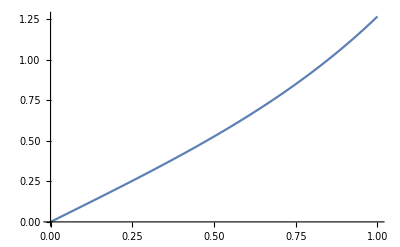

```mathematica
Plot[ Evaluate[ y[x] /. Flatten[NDSolve[ eq4pt3pt25  /. y0-> 0 /. yprime0-> 1  , y[x] , { x , 0, 1 } ] ] ], { x , 0 , 1 } ]
```

```mathematica
Clear[eq4pt3pt35]
eq4pt3pt35 = {
y''[x] == y[x]^2+ Exp[x] , 
y'[0] == yprime0 , 
y[0] == y0 
} ;
eq4pt3pt35 // TableForm
```

y''[x]==ⅇ^x+y[x]^2
y'[0]==yprime0
y[0]==y0

```mathematica
eq4pt3pt35  /. y0-> 0 /. yprime0 -> 0
```

{y''[x]==ⅇ^x+y[x]^2,y'[0]==0,y[0]==0}

```mathematica
Clear[eq4pt4pt5]
eq4pt4pt5 = { 
y1'[x] == y1[x] - y1[x] y2[x] , 
y2'[x] == - y2[x] + y1[x] y2[x]
} ;
eq4pt4pt5  // TableForm
```

y1'[x]==y1[x]-y1[x] y2[x]
y2'[x]==-y2[x]+y1[x] y2[x]

```mathematica
Clear[A] (* I don't think this is right *) 
A = 
{ Coefficient[ eq4pt4pt5 [[1,2]] , { y1[x] , y2[x] } ]  , 
Coefficient[ eq4pt4pt5 [[2,2]] ,  { y1[x] , y2[x] } ] }
```

{{1-y2[x],-y1[x]},{y2[x],-1+y1[x]}}

```mathematica
Flatten[Solve[ Det[A - λ IdentityMatrix[2]] == 0 , λ ] ] // TableForm
```

λ→1/2 (y1[x]-y2[x]-√((-y1[x]+y2[x])^2-4 (-1+y1[x]+y2[x])))
λ→1/2 (y1[x]-y2[x]+√((-y1[x]+y2[x])^2-4 (-1+y1[x]+y2[x])))

```mathematica
Clear[eq4pt4pt6]
eq4pt4pt6 = { 
y1'[x] == y1[x] ( 3 - y1[x] - y2[x] ) , 
y1[0] == y10 , 
y2'[x] == y2[x] ( y1[x]-1 )  , 
y2[0] == y20
} ;
eq4pt4pt6 // TableForm
```

y1'[x]==y1[x] (3-y1[x]-y2[x])
y1[0]==y10
y2'[x]==(-1+y1[x]) y2[x]
y2[0]==y20

```mathematica
eq4pt4pt6 /. y10-> 0  /. y20-> 0
```

{y1'[x]==y1[x] (3-y1[x]-y2[x]),y1[0]==0,y2'[x]==(-1+y1[x]) y2[x],y2[0]==0}

```mathematica
Clear[eq4pt4pt6Sol]
eq4pt4pt6Sol = 
Flatten[NDSolve[ eq4pt4pt6  /. y10-> 0 /. y20-> 0  , { y1[x] , y2[x] } , { x , 0 , 10 } ]]
```

{y1[x]→InterpolatingFunction[…][x],y2[x]→InterpolatingFunction[…][x]}

```mathematica
?ParametricPlot
```

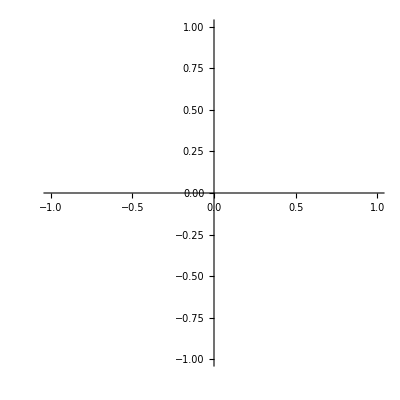

```mathematica
ParametricPlot[ 
Evaluate[
{y1[x] , y2[x] } /. eq4pt4pt6Sol ] , { x , 0 , 10 } ]
```

```mathematica
Clear[eq4pt4pt7]
eq4pt4pt7 = { 
y1'[x] == y1[x]^2+ y1[x] y2[x] - y1[x] , 
y2'[x] == y2[x]^2+ y1[x] y2[x] - 2 y2[x] 
} ;
eq4pt4pt7
```

{y1'[x]==-y1[x]+y1[x]^2+y1[x] y2[x],y2'[x]==-2 y2[x]+y1[x] y2[x]+y2[x]^2}

```mathematica
NDSolve[ Union[ eq4pt4pt7   , {y1[0] == 1 , y2[0] == 1 }] , { y1[x] , y2[x] } , x ]
```

{{y1[x]→InterpolatingFunction[…][x],y2[x]→InterpolatingFunction[…][x]}}

```mathematica
Clear[eq4pt4pt8]
eq4pt4pt8 = { 
y1'[x] == y1[x] + y2[x] - y1[x] ( y1[x]^2+ y2[x]^2) , 
y2'[x] == -y1[x] + y2[x] - y2[x] ( y1[x]^2 + y2[x]^2) 
} ;
eq4pt4pt8 // TableForm
```

y1'[x]==y1[x]+y2[x]-y1[x] (y1[x]^2+y2[x]^2)
y2'[x]==-y1[x]+y2[x]-y2[x] (y1[x]^2+y2[x]^2)

```mathematica
NDSolve[ Union[ eq4pt4pt8   , {y1[0] == 1 , y2[0] == 1 }] , { y1[x] , y2[x] } , x ]
```

{{y1[x]→InterpolatingFunction[…][x],y2[x]→InterpolatingFunction[…][x]}}

```mathematica
Clear[eq4pt4pt9]
eq4pt4pt9 = { 
y1'[t] == - y2[t] + y1[t] ( y1[t]^2+ y2[t]^2)  , 
y2'[t] ==  y1[t] + y2[t] ( y1[t]^2+ y2[t]^2)  , 
y1[0] == y10 , 
y2[0] == y20 
} ;
eq4pt4pt9 // TableForm
```

y1'[t]==-y2[t]+y1[t] (y1[t]^2+y2[t]^2)
y2'[t]==y1[t]+y2[t] (y1[t]^2+y2[t]^2)
y1[0]==y10
y2[0]==y20

```mathematica
Clear[eq4pt4pt9Sol]
eq4pt4pt9Sol = 
Flatten[NDSolve[ eq4pt4pt9  /. y10-> 1 /. y20 -> 1  , { y1[t] , y2[t] } , {t , 0 , 0.5 } ]]
```

{y1[t]→InterpolatingFunction[…][t],y2[t]→InterpolatingFunction[…][t]}

```mathematica
ParametricPlot[
Evaluate[
{y1[t],y2[t] } /. eq4pt4pt9Sol] , { t , 0 , 0.5 } ]
```

-Graphics-

```mathematica
Clear[eq4pt5pt10]
eq4pt5pt10 = {
x'[t] == -3 ( x[t] - y[t] )  , 
x[0] == x0 
};

Clear[eq4pt5pt11]
eq4pt5pt11 =  {
y'[t] == -x[t] z[t] + r x[t] - y[t]  , 
y[0] == y0 
} ;

Clear[eq4pt5pt12]
eq4pt5pt12 =  {
z'[t] == x[t] y[t] - z[t] , 
z[0] == z0 
} ;
```

```mathematica
eq4pt5pt11  /. r-> 26  (* Plot 4pt27 page 195 *)
```

{y'[t]==26 x[t]-y[t]-x[t] z[t],y[0]==y0}

```mathematica
Clear[lorenz1] (* Initial conditions given in figure 4pt27 page 195 *) 
lorenz1 = 
NDSolve[ Union[ ( eq4pt5pt10 /. x0-> 0 )   ,  
( eq4pt5pt11 /. r-> 26 /. y0-> 1   )   ,  
( eq4pt5pt12  /. z0-> 0 )] , 
{ x[t] ,y[t] , z[t] } , { t , 0 , 100 } ]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

```mathematica
ParametricPlot3D[
Evaluate[{x[t],y[t],z[t]} /. lorenz1] , { t, 0, 100 } , PlotPoints-> 10000 , 
AxesLabel-> {"x[t]" , "y[t]" , "z[t]" }   ]
```

-Graphics3D-

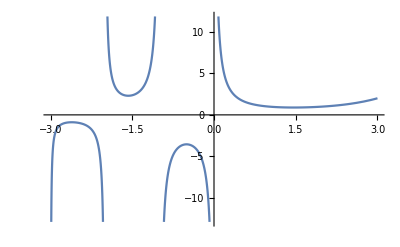

```mathematica
Plot[Gamma[x],{x,-3,3}]
```

```mathematica
?StirlingS2
```

```mathematica
Table[StirlingS1[10,m],{m,10}]
Table[StirlingS2[10,m],{m,10}]
```

{-362880,1026576,-1172700,723680,-269325,63273,-9450,870,-45,1}

{1,511,9330,34105,42525,22827,5880,750,45,1}

```mathematica
?AsymptoticIntegrate
```

```mathematica
(* Page 250 *) 
(* Example 1 *) 
AsymptoticIntegrate[Sin[t x]/t, {t,0,1},{x,0,5}]
```

x-x^3/18+x^5/600

```mathematica
(* Page 250 *) 
(* Example 2 *) 
AsymptoticIntegrate[Exp[-t]/(√t), {t,0,x},{x,0,5}]
```

2 √x-(2 x^(3/2))/3+x^(5/2)/5-x^(7/2)/21+x^(9/2)/108-x^(11/2)/660

```mathematica
(* Page 251 *)  
(* Example 3 *) 
Integrate[ Exp[-t^4] , { t , 0 , ∞ } ] -
AsymptoticIntegrate[Exp[-t^4], {t,0,x},{x,0,13}]
```

-x+x^5/5-x^9/18+x^13/78+Gamma[5/4]

```mathematica
(* Page 276 *) 
(* Example 1 *) 
AsymptoticIntegrate[Exp[ⅈ x t]/(1+t), {t,0,1},{x,0,5}]
```

-ⅈ x (-1+Log[2])+Log[2]+1/288 x^4 (-7+12 Log[2])-(ⅈ x^5 (-47+60 Log[2]))/7200-1/4 x^2 (-1+Log[4])+1/36 ⅈ x^3 (-5+Log[64])

## Chapter 6

```mathematica
Clear[eq6pt5pt3] (* This is wrong, do again *) 
eq6pt5pt3 = 
-(ⅈ/x) Exp[ⅈ x] + (ⅈ/(2 x)) AsymptoticIntegrate[Exp[ⅈ x t]/(1+t), {t,0,1},{x,0,5}]
```

-(ⅈ ⅇ^(ⅈ x))/x+1/(2 x)ⅈ (-ⅈ x (-1+Log[2])+Log[2]+1/288 x^4 (-7+12 Log[2])-(ⅈ x^5 (-47+60 Log[2]))/7200-1/4 x^2 (-1+Log[4])+1/36 ⅈ x^3 (-5+Log[64]))

```mathematica
Clear[eq6pt6pt3]
eq6pt6pt3 = 
AsymptoticIntegrate[Log[t] Exp[ⅈ x t], {t,0,1},{x,0,5}]
```

-1-(ⅈ x)/4+x^2/18+(ⅈ x^3)/96-x^4/600-(ⅈ x^5)/4320

```mathematica
Clear[eq6pt6pt10]
eq6pt6pt10 = 
AsymptoticIntegrate[ Exp[ⅈ x Exp[-1/s]], {s,0,1},{x,0,5}]
```

1+(ⅈ x (1+ⅇ ExpIntegralEi[-1]))/ⅇ+(x^2 (-1+2 ⅇ^2 Gamma[0,2]))/(2 ⅇ^2)+(ⅈ x^3 (-1+3 ⅇ^3 Gamma[0,3]))/(6 ⅇ^3)-(x^4 (-1+4 ⅇ^4 Gamma[0,4]))/(24 ⅇ^4)-(ⅈ x^5 (-1+5 ⅇ^5 Gamma[0,5]))/(120 ⅇ^5)

```mathematica
(* Page 289 *) 
(* Example 4 *)
```

```mathematica
Re[  Expand[ ρ[t] == z^2 /. z-> u + ⅈ v ][[2]]  ]
Expand[ ρ[t] == t^2 /. t-> u + ⅈ v ][[2]]
```

-2 Im[u v]+Re[u^2-v^2]

u^2+2 ⅈ u v-v^2

```mathematica
AsymptoticSum[1/k,{k,1,n},n->∞]
```

Log[n]

```mathematica
Clear[eq6pt7pt4a]
eq6pt7pt4a = 
AsymptoticSum[ ( k^α /. α-> 0 ) ,  { k , 1, n } , n-> ∞ ]
```

n

```mathematica
Clear[eq6pt7pt4b]
eq6pt7pt4b = 
AsymptoticSum[ ( k^α /. α-> -1 ) ,  { k , 1, n } , n-> ∞ ]
```

Log[n]

```mathematica
Clear[eq6pt7pt4b]
eq6pt7pt4b = 
AsymptoticSum[ ( k^α /. α-> -2 ) ,  { k , 1, n } , n-> ∞ ]

Zeta[-(-2)]
```

π^2/6

π^2/6

```mathematica
?AsymptoticSum
```

```mathematica
(* Example 6 page 306  no idea if this is right *)  
AsymptoticSum[Log[ k! ] ,{k,1,n},n->∞]
```

Log[ⅇ^(1/(12 n)+1/4 n^2 (-3+2 Log[n])+1/2 n (-2+2 Log[n]+Log[2 π])+1/12 (1-12 Log[Glaisher]+5 Log[n]+6 Log[2 π]))]

```mathematica
Clear[problem6pt7a]
problem6pt7a = 
AsymptoticIntegrate[ Cos[ x t ] , {t,x,1},{x,0,5}]
```

1-x-x^2/6+x^4/120+x^5/6

```mathematica
Clear[problem6pt7b]
problem6pt7b = 
AsymptoticIntegrate[Sqrt[ Sinh[x t ] ]  , {t,0,1},{x,0,5}]
```

(2 √x)/3+x^(5/2)/42+x^(9/2)/7920

```mathematica
Clear[problem6pt7c]
problem6pt7c = 
AsymptoticIntegrate[Exp[-x / t ]  , {t,0,1},{x,0,5}]
```

1-x^2/2+x^3/12-x^4/72+x^5/480+x (-1+EulerGamma+Log[x])

```mathematica
Clear[problem6pt7d]
problem6pt7d = 
AsymptoticIntegrate[ Exp[-1/t] , {t,x,1},{x,0,5}]
```

ⅇ^(-1/x) (-x^2+2 x^3-6 x^4+24 x^5)+(1+ⅇ ExpIntegralEi[-1]+ⅇ Log[1/x]+ⅇ Log[x])/ⅇ

```mathematica
Clear[problem6pt7e]
problem6pt7e = 
AsymptoticIntegrate[ Sin[ x t ] , {t,x,1},{x,0,5}]
```

x/2-(13 x^3)/24+x^5/720

```mathematica
Clear[problem6pt7g]
problem6pt7g = 
AsymptoticIntegrate[ Exp[-t^2] , {t,0,1/x},{x,0,5}]
```

1/2 ((-1)^Floor[(π+2 Arg[x])/(2 π)] √π+ⅇ^(-1/x^2) (-x+x^3/2-(3 x^5)/4))

```mathematica
Clear[problem6pt8a]
problem6pt8a = 
AsymptoticIntegrate[Exp[-t]/(1+x^2 t^3) , {t,0,1},{x,0,5}]
```

(-1+ⅇ)/ⅇ-(2 (-8+3 ⅇ) x^2)/ⅇ+((-1957+720 ⅇ) x^4)/ⅇ

```mathematica
Clear[problem6pt56a]
problem6pt56a = 
AsymptoticIntegrate[ Exp[ⅈ x t^2] Cosh[t^2] , {t,0,1},{x,0,5}]
```

1/4 √π (Erf[1]+Erfi[1])+1/8 ⅈ x (√π Erf[1]-√π Erfi[1]+4 Sinh[1])-1/32 x^2 (-12 Cosh[1]+3 √π Erf[1]+3 √π Erfi[1]+8 Sinh[1])-1/192 ⅈ x^3 (-40 Cosh[1]+15 √π Erf[1]-15 √π Erfi[1]+76 Sinh[1])+(x^4 (-532 Cosh[1]+105 √π Erf[1]+105 √π Erfi[1]+312 Sinh[1]))/1536+(ⅈ x^5 (-2808 Cosh[1]+945 √π Erf[1]-945 √π Erfi[1]+4852 Sinh[1]))/15360

## Chapter 7

```mathematica
Clear[eq7pt1pt1]
eq7pt1pt1 = 
x^3- 4.001 x + 0.002
```

0.002-4.001 x+x^3

```mathematica
Clear[eq7pt1pt2]
eq7pt1pt2 = 
x^3- (4+ ε ) x + 2 ε
```

x^3+2 ε-x (4+ε)

```mathematica
Clear[eq7pt1pt3]
eq7pt1pt3[n_]:= 
x-> Sum[ a[k] ε^k , { k , 0 , n } ]
```

```mathematica
eq7pt1pt3[1]
eq7pt1pt3[2]
eq7pt1pt3[3]
```

x→a[0]+ε a[1]

x→a[0]+ε a[1]+ε^2 a[2]

x→a[0]+ε a[1]+ε^2 a[2]+ε^3 a[3]

```mathematica
Clear[eq7pt1pt2eqs]
eq7pt1pt2eqs = 
Table[
Thread[ 
CoefficientList[ Expand[ eq7pt1pt2  /. eq7pt1pt3[3] ]   , ε ][[i]] == 0 ], 
{ i , 1 , 
Length[  CoefficientList[ Expand[ eq7pt1pt2  /. eq7pt1pt3[3] ]   , ε ]]}] ;

Flatten[eq7pt1pt2eqs] // TableForm
```

-4 a[0]+a[0]^3==0
2-a[0]-4 a[1]+3 a[0]^2 a[1]==0
-a[1]+3 a[0] a[1]^2-4 a[2]+3 a[0]^2 a[2]==0
a[1]^3-a[2]+6 a[0] a[1] a[2]-4 a[3]+3 a[0]^2 a[3]==0
3 a[1]^2 a[2]+3 a[0] a[2]^2-a[3]+6 a[0] a[1] a[3]==0
3 a[1] a[2]^2+3 a[1]^2 a[3]+6 a[0] a[2] a[3]==0
a[2]^3+6 a[1] a[2] a[3]+3 a[0] a[3]^2==0
3 a[2]^2 a[3]+3 a[1] a[3]^2==0
3 a[2] a[3]^2==0
a[3]^3==0

```mathematica
Solve[ eq7pt1pt2eqs[[1]]  , a[0] ] 
Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[1]] 
Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[2]] 
Solve[ eq7pt1pt2eqs[[1]]  , a[0] ] [[3]]
```

{{a[0]→-2},{a[0]→0},{a[0]→2}}

{a[0]→-2}

{a[0]→0}

{a[0]→2}

```mathematica
eq7pt1pt2eqs[[2]]
Solve[ eq7pt1pt2eqs[[2]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[1]]  , a[1] ] 
Solve[ eq7pt1pt2eqs[[2]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[2]]  , a[1] ] 
Solve[ eq7pt1pt2eqs[[2]]/. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[3]]  , a[1] ]
```

2-a[0]-4 a[1]+3 a[0]^2 a[1]==0

{{a[1]→-1/2}}

{{a[1]→1/2}}

{{a[1]→0}}

```mathematica
eq7pt1pt2eqs[[3]]

Solve[ eq7pt1pt2eqs[[3]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[1]]  /. Solve[ eq7pt1pt2eqs[[2]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[1]]  , a[1] ]   , a[2]]

Solve[ eq7pt1pt2eqs[[3]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[2]]  /. Solve[ eq7pt1pt2eqs[[2]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[2]]  , a[1] ]  , a[2]]

Solve[ eq7pt1pt2eqs[[3]] /. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ] [[3]]  /. Solve[ eq7pt1pt2eqs[[2]]/. Solve[ eq7pt1pt2eqs[[1]]  , a[0] ][[3]]  , a[1] ]  , a[2] ]
```

-a[1]+3 a[0] a[1]^2-4 a[2]+3 a[0]^2 a[2]==0

{{a[2]→1/8}}

{{a[2]→-1/8}}

{{a[2]→0}}

```mathematica
Clear[eq7pt1pt9]
eq7pt1pt9[n_]:= 
y[x]-> Sum[ ε^k y[k][x] , { k , 0 , n } ]
```

```mathematica
eq7pt1pt9[5]
D[ eq7pt1pt9[5] , x ] 
D[ eq7pt1pt9[5] , { x , 2 } ]
```

y[x]→y[0][x]+ε y[1][x]+ε^2 y[2][x]+ε^3 y[3][x]+ε^4 y[4][x]+ε^5 y[5][x]

y'[x]→y[0]'[x]+ε y[1]'[x]+ε^2 y[2]'[x]+ε^3 y[3]'[x]+ε^4 y[4]'[x]+ε^5 y[5]'[x]

y''[x]→y[0]''[x]+ε y[1]''[x]+ε^2 y[2]''[x]+ε^3 y[3]''[x]+ε^4 y[4]''[x]+ε^5 y[5]''[x]

```mathematica
Clear[eq7pt1pt15]
eq7pt1pt15 = {
y''[x]  +  Exp[-x] y[x]== 0  , 
y[0] == 1 , 
y'[0] == 1 
} ;
eq7pt1pt15
```

{ⅇ^-x y[x]+y''[x]==0,y[0]==1,y'[0]==1}

```mathematica
DSolve[ eq7pt1pt15  , y[x] , x ]
```

{{y[x]→(BesselJ[0,2 √(ⅇ^-x)] BesselY[0,2]-BesselJ[0,2] BesselY[0,2 √(ⅇ^-x)]+BesselJ[1,2] BesselY[0,2 √(ⅇ^-x)]-BesselJ[0,2 √(ⅇ^-x)] BesselY[1,2])/(BesselJ[1,2] BesselY[0,2]-BesselJ[0,2] BesselY[1,2])}}

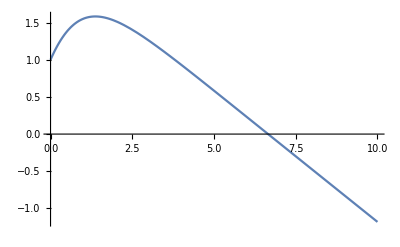

```mathematica
Plot[
Evaluate[ 
y[x]  /. DSolve[ eq7pt1pt15  , y[x] , x ]  ] , { x , 0 , 10 } ]
```

```mathematica
eq7pt1pt15[[1]]
eq7pt1pt15[[2]] /. Equal-> Rule 
eq7pt1pt15[[3]] /. Equal-> Rule
```

y''[x]==-ⅇ^-x y[x]

y[0]→1

y'[0]→1

```mathematica
eq7pt1pt15[[1,1]]
```

ⅇ^-x y[x]+y''[x]

```mathematica
CoefficientList[(eq7pt1pt15[[1,1]]  /. eq7pt1pt9[3] /. D[  eq7pt1pt9[3] , {x,2}] // Expand  ) , ε ]  // TableForm
```

ⅇ^-x y[0][x]+y[0]''[x]
ⅇ^-x y[1][x]+y[1]''[x]
ⅇ^-x y[2][x]+y[2]''[x]
ⅇ^-x y[3][x]+y[3]''[x]

```mathematica
Clear[eq7pt2pt1]
eq7pt2pt1 = 
ε^2 x^6 - ε x^4 - x^3 + 8
```

8-x^3-x^4 ε+x^6 ε^2

```mathematica
Solve[ ( eq7pt2pt1 /. ε-> 0  ) == 0 , x ]
```

{{x→2},{x→-2 (-1)^(1/3)},{x→2 (-1)^(2/3)}}

```mathematica
Clear[eq7pt2pt7]
eq7pt2pt7 =  { 
ε y''[x] - y'[x] == 0  , 
y[0] == 0 , 
y[1] == 0 
} ;
eq7pt2pt7
```

{-y'[x]+ε y''[x]==0,y[0]==0,y[1]==0}

```mathematica
DSolve[ eq7pt2pt7 , y[x] , x ]  /. C[1]-> 1
```

{{y[x]→Piecewise[{{1-ⅇ^(x/ε), ε==ⅇ^(1/ε) ε}, {0, True}}]}}

```mathematica
Clear[eq7pt2pt11]
eq7pt2pt11 = {
y''[x] + ( 1 - ε x ) y[x] == 0 ,
y[0] == 0 , 
y'[0] == 0 
} ;
eq7pt2pt11 // TableForm
```

(1-x ε) y[x]+y''[x]==0
y[0]==0
y'[0]==0

```mathematica
DSolve[ eq7pt2pt11 , y[x] , x ]
```

{{y[x]→Piecewise[{{(-(AiryAi[(-1+x ε)/ε^(2/3)] AiryBi[-1/ε^(2/3)])/AiryAi[-1/ε^(2/3)]+AiryBi[(-1+x ε)/ε^(2/3)]) C[1], ε^(1/3)==0}, {0, True}}]}}

```mathematica
eq7pt1pt9[3]
D[ eq7pt1pt9[3] , x ] 
D[ eq7pt1pt9[3] , { x , 2 }  ] 
Table[ 
Thread[y[n][0] == 1   ] , {n , 0 , 3 } ] 
Table[ 
Thread[y[n]'[0]  ==  0] , {n , 0 , 3 } ] 
Clear[eq7pt1pt9ics]
eq7pt1pt9ics = 
Table[ 
{ y[n][0] == 1, y[n]'[0] == 0 } , { n , 0 , 3 } ]
```

y[x]→y[0][x]+ε y[1][x]+ε^2 y[2][x]+ε^3 y[3][x]

y'[x]→y[0]'[x]+ε y[1]'[x]+ε^2 y[2]'[x]+ε^3 y[3]'[x]

y''[x]→y[0]''[x]+ε y[1]''[x]+ε^2 y[2]''[x]+ε^3 y[3]''[x]

{y[0][0]==1,y[1][0]==1,y[2][0]==1,y[3][0]==1}

{y[0]'[0]==0,y[1]'[0]==0,y[2]'[0]==0,y[3]'[0]==0}

{{y[0][0]==1,y[0]'[0]==0},{y[1][0]==1,y[1]'[0]==0},{y[2][0]==1,y[2]'[0]==0},{y[3][0]==1,y[3]'[0]==0}}

```mathematica
Clear[eq7pt2pt11eqs]
eq7pt2pt11eqs = 
Thread[
CoefficientList[
Expand[ eq7pt2pt11[[1,1]] /. eq7pt1pt9[3] /. D[ eq7pt1pt9[3] , { x , 2 }  ] ] , ε ] == 0 ]  ;
eq7pt2pt11eqs // TableForm
```

y[0][x]+y[0]''[x]==0
-x y[0][x]+y[1][x]+y[1]''[x]==0
-x y[1][x]+y[2][x]+y[2]''[x]==0
-x y[2][x]+y[3][x]+y[3]''[x]==0
-x y[3][x]==0

```mathematica
DSolve[ Union[
{eq7pt1pt9eqs[[1]]} , 
eq7pt1pt9ics[[1]]
] , 
y[0][x] , x ]
```

DSolve[{y[0][0]==1,y[0]'[0]==0,y[0][x]+y[0]''[x]},y[0][x],x]

```mathematica
∏_(k=1)^20 ((x-k) + ε x^19) (* can't tell if ε is part of the product or added afterwards *)
```

(-20+x+x^19 ε) (-19+x+x^19 ε) (-18+x+x^19 ε) (-17+x+x^19 ε) (-16+x+x^19 ε) (-15+x+x^19 ε) (-14+x+x^19 ε) (-13+x+x^19 ε) (-12+x+x^19 ε) (-11+x+x^19 ε) (-10+x+x^19 ε) (-9+x+x^19 ε) (-8+x+x^19 ε) (-7+x+x^19 ε) (-6+x+x^19 ε) (-5+x+x^19 ε) (-4+x+x^19 ε) (-3+x+x^19 ε) (-2+x+x^19 ε) (-1+x+x^19 ε)

```mathematica
Clear[eq7pt3pt4]
eq7pt3pt4 = 
-y''[x] + (x^2 y[x])/4- ℰ y[x] == 0
```

1/4 x^2 y[x]-ℰ y[x]-y''[x]==0

```mathematica
DSolve[ ( eq7pt3pt4  /. ℰ -> ( n + 1/2 )  /. n-> 0  ) , y[x] , x ]  /. C[1]-> 1 /. C[2] -> 1
```

{{y[x]→ⅇ^(-x^2/4)+ⅇ^(-x^2/4) √(π/2) Erfi[x/(√2)]}}

```mathematica
Clear[eq7pt4pt1]
eq7pt4pt1 = 
y''[x] - y[x] == Exp[-Abs[x]]
```

-y[x]+y''[x]==ⅇ^(-Abs[x])

```mathematica
DSolve[ eq7pt4pt1  , y[x]  , x ]   /. C[2]-> 0   (* No idea what this solution refers to *)
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x (ⅇ^(2 x) 1/2 ⅇ^(-Abs[K[1]]-K[1])K[1]1x+-1/2 ⅇ^(-Abs[K[2]]+K[2])K[2]1x)}}

```mathematica
Clear[eq7pt4pt3a]
eq7pt4pt3a =  { 
y'[x] + ( ε x^2 + 1 + k/x^2) y[x] == 0 , 
y[1] == 1
} ;
eq7pt4pt3a // TableForm
```

(1+k/x^2+x^2 ε) y[x]+y'[x]==0
y[1]==1

```mathematica
eq7pt4pt3a    /. k-> 0
```

{(1+x^2 ε) y[x]+y'[x]==0,y[1]==1}

```mathematica
Flatten[DSolve[ eq7pt4pt3a   /. k-> 1  , y[x] , x ]]
```

{y[x]→ⅇ^(1/x-x+ε/3-(x^3 ε)/3)}

```mathematica
Clear[problem7pt1a]
problem7pt1a = 
x^2+ x + 6 ε
```

x+x^2+6 ε

```mathematica
eq7pt1pt3[2]
```

x→a[0]+ε a[1]+ε^2 a[2]

```mathematica
Clear[problem7pt1aeqs]
problem7pt1aeqs = 
Thread[
CoefficientList[ problem7pt1a  //. eq7pt1pt3[2] // Expand  , ε ]  == 0 ]
```

{a[0]+a[0]^2==0,6+a[1]+2 a[0] a[1]==0,a[1]^2+a[2]+2 a[0] a[2]==0,2 a[1] a[2]==0,a[2]^2==0}

```mathematica
Solve[ problem7pt1aeqs [[1]] , a[0] ][[1]]
```

{a[0]→-1}

```mathematica
Solve[ problem7pt1aeqs[[2]] /. Solve[ problem7pt1aeqs [[1]] , a[0] ][[1]]  , a[1] ]
```

{{a[1]→6}}

```mathematica
Solve[ problem7pt1aeqs[[3]] /. Solve[ problem7pt1aeqs [[1]] , a[0] ][[1]] /. Solve[ problem7pt1aeqs[[2]] /. Solve[ problem7pt1aeqs [[1]] , a[0] ][[1]]  , a[1] ]  , a[2] ]
```

{{a[2]→36}}

```mathematica
eq7pt1pt3[2] /. {a[0]->-1} /. {{a[1]->6}} /. {{a[2]->36}} /. ε-> -0.01
```

{{x→-1.0564}}

```mathematica
Solve[( problem7pt1  /. ε-> -0.01 )== 0 ]
```

{{x→-1.05678},{x→0.0567764}}

```mathematica
Clear[problem7pt1b]
problem7pt1b = 
x^3- ε x - 1
```

-1+x^3-x ε

```mathematica
Clear[problem7pt1beqs]
problem7pt1beqs = 
Thread[CoefficientList[Expand[problem7pt1b /. eq7pt1pt3[2]] , ε ]== 0 ]
```

{-1+a[0]^3==0,-a[0]+3 a[0]^2 a[1]==0,-a[1]+3 a[0] a[1]^2+3 a[0]^2 a[2]==0,a[1]^3-a[2]+6 a[0] a[1] a[2]==0,3 a[1]^2 a[2]+3 a[0] a[2]^2==0,3 a[1] a[2]^2==0,a[2]^3==0}

```mathematica
Solve[ problem7pt1beqs[[1]] , a[0] ][[1]]
```

{a[0]→1}

```mathematica
Solve[ problem7pt1beqs[[2]] /. Solve[ problem7pt1beqs[[1]] , a[0] ][[1]]  , a[1]]
```

{{a[1]→1/3}}

```mathematica
Solve[
( problem7pt1beqs[[3]] /. Solve[ problem7pt1beqs[[1]] , a[0] ][[1]]  /. Solve[ problem7pt1beqs[[2]] /. Solve[ problem7pt1beqs[[1]] , a[0] ][[1]]  , a[1]] ) , 
a[2] ]
```

{{a[2]→0}}

```mathematica
eq7pt1pt3[2] /. {a[0]->1} /. {{a[1]->1/3}} /. {{a[2]->0}}
```

{{x→1+ε/3}}

```mathematica
{x->1+ε/3} /. ε -> 0.01
```

{x→1.00333}

```mathematica
Solve[ (problem7pt1b  /. ε-> 0.01 ) == 0 ]
```

{{x→-0.501667-0.863139 ⅈ},{x→-0.501667+0.863139 ⅈ},{x→1.00333}}

```mathematica
Clear[problem7pt1c]
problem7pt1c = 
x^3+ ε x^2-x
```

-x+x^3+x^2 ε

```mathematica
Clear[problem7pt1ceqs]
problem7pt1ceqs = 
Thread[CoefficientList[Expand[problem7pt1c  /. eq7pt1pt3[2]] , ε ] == 0 ]
```

{-a[0]+a[0]^3==0,a[0]^2-a[1]+3 a[0]^2 a[1]==0,2 a[0] a[1]+3 a[0] a[1]^2-a[2]+3 a[0]^2 a[2]==0,a[1]^2+a[1]^3+2 a[0] a[2]+6 a[0] a[1] a[2]==0,2 a[1] a[2]+3 a[1]^2 a[2]+3 a[0] a[2]^2==0,a[2]^2+3 a[1] a[2]^2==0,a[2]^3==0}

```mathematica
Solve[ problem7pt1ceqs[[1]] , a[0] ][[3]]  (* not sure how to know which one to pick? corresponds to three different roots *)
```

{a[0]→1}

```mathematica
Solve[ problem7pt1ceqs[[2]] /. Solve[ problem7pt1ceqs[[1]] , a[0] ][[3]]   , a[1] ]
```

{{a[1]→-1/2}}

```mathematica
Solve[ ( problem7pt1ceqs[[3]] /. Solve[ problem7pt1ceqs[[1]] , a[0] ][[3]]  /. Solve[ problem7pt1ceqs[[2]] /. Solve[ problem7pt1ceqs[[1]] , a[0] ][[3]]   , a[1] ] ) , a[2]]
```

{{a[2]→1/8}}

```mathematica
eq7pt1pt3[2] /. {a[0]->1} /. {a[1]->-1/2} /. {a[2]->1/8}
 eq7pt1pt3[2] /. {a[0]->1} /. {a[1]->-1/2} /. {a[2]->1/8} /. ε -> 0.01
```

x→1-ε/2+ε^2/8

x→0.995013

```mathematica
Solve[ ( problem7pt1c /. ε -> 0.01 ) == 0 ][[3]]
```

{x→0.995012}

```mathematica
Clear[problem7pt4]
problem7pt4 = 
x^3-x^2+ ε
```

-x^2+x^3+ε

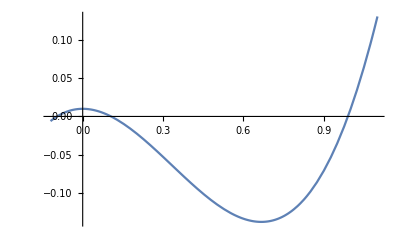

```mathematica
Plot[ ( problem7pt4 /. ε-> 0.01 ) , { x , -0.12 , 1.1 } ] 
(* Three real roots *)
```

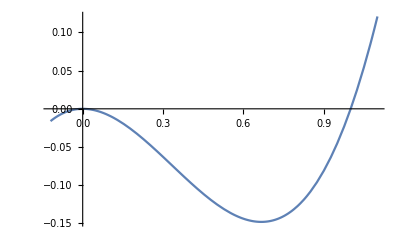

```mathematica
Plot[ ( problem7pt4 /. ε-> 0 ) , { x , -0.12 , 1.1 } ] 
(* One repeated, other real *)
```

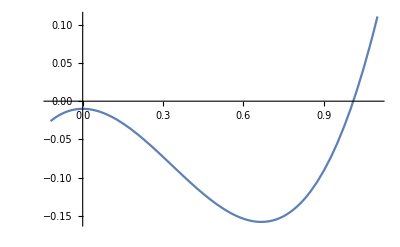

```mathematica
Plot[ ( problem7pt4 /. ε->- 0.01) , { x , -0.12 , 1.1 } ] 
(* One real - conjuage imaginary pair  *)
```

```mathematica
Clear[problem7pt5a]
problem7pt5a = 
Manipulate[
Plot[
Evaluate[
ε x^3 + x^2 - 2 x + 1 ] , { x , - xmax , xmax } , 
PlotRange-> {-ymax,ymax} ,
PlotLabel-> "problem7pt5a"

] , {ε , -0.2 , 0.2 }  , { xmax, 1 , 10 }  , {ymax, 1 , 10 } ]
```

```mathematica
Clear[problem7pt5b]
problem7pt5b = 
Manipulate[
Plot[
Evaluate[
ε x^8 + ε^2 x^6 + x - 2 ] , { x , - xmax , xmax } , 
PlotRange-> {-ymax,ymax},
PlotLabel->"problem7pt5b"
] , {ε , -0.2 , 0.2 }  , { xmax, 1 , 5 }  , {ymax, 1 , 10 } ]
```

```mathematica
Clear[problem7pt5c]
problem7pt5c = 
Manipulate[
Plot[
Evaluate[
ε^2 x^8 + ε x^6 + x - 2 ] , { x , - xmax , xmax } , 
PlotRange-> {-ymax,ymax},
PlotLabel->"problem7pt5c"
] , {ε , -0.2 , 0.2 }  , { xmax, 1 , 10 }  , {ymax, 1 , 20 } ]
```

```mathematica
Clear[problem7pt36]
problem7pt36 = 
AsymptoticIntegrate[Exp[ⅈ x t^2] Cos[t]  , {t,0,π},{x,0,5}]
```

-2 ⅈ π x+2 π (-6+π^2) x^2+ⅈ π (120-20 π^2+π^4) x^3-1/3 π (-5040+840 π^2-42 π^4+π^6) x^4-1/12 ⅈ π (362880-60480 π^2+3024 π^4-72 π^6+π^8) x^5

```mathematica
Clear[problem7pt36]
problem7pt36 = 
AsymptoticIntegrate[Exp[ⅈ x t^4] Cos[t]  , {t,0,π},{x,0,5}]
```

-4 ⅈ π (-6+π^2) x+4 π (-5040+840 π^2-42 π^4+π^6) x^2+2 ⅈ π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10) x^3-2/3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14) x^4-1/6 ⅈ π (-121645100408832000+20274183401472000 π^2-1013709170073600 π^4+24135932620800 π^6-335221286400 π^8+3047466240 π^10-19535040 π^12+93024 π^14-342 π^16+π^18) x^5

## Chapter 8

```mathematica
Clear[eq8pt12]
eq8pt12[n_] := 
A[n]  ==A +  α q^n
```

```mathematica
{eq8pt12[n-1] , eq8pt12[n] , eq8pt12[n+1] }  // TableForm
```

A[-1+n]==A+q^(-1+n) α
A[n]==A+q^n α
A[1+n]==A+q^(1+n) α

```mathematica
Clear[ eq8pt12System]
eq8pt12System = { 
Eliminate[ {eq8pt12[n-1] , eq8pt12[n] , eq8pt12[n+1] }  , α ][[1]]  , 
Simplify[Eliminate[ {eq8pt12[n-1] , eq8pt12[n] , eq8pt12[n+1] }  , α ][[2]]][[1,2]] == 0 
} ;
eq8pt12System  // TableForm
```

A[n]==A-A q+q A[-1+n]
A (-1+q^2)-q^2 A[-1+n]+A[1+n]==0

```mathematica
Clear[eq8pt1pt2a]
eq8pt1pt2a = 
Flatten[Solve[ Eliminate[ eq8pt12System , q ]  , A ]]
```

{A→(-A[n]^2+A[-1+n] A[1+n])/(A[-1+n]-2 A[n]+A[1+n])}

```mathematica
?Nest
```

```mathematica
?RSolve
```

```mathematica
Clear[eq8pt2pt2]
eq8pt2pt2[n_]:= 
Sum[(a[k] x^k)/(k!), { k , 0 , n } ]
```

```mathematica
eq8pt2pt2[4]
```

a[0]+x a[1]+1/2 x^2 a[2]+1/6 x^3 a[3]+1/24 x^4 a[4]

```mathematica
Integrate[ Expand[Exp[-t]( eq8pt2pt2[4] /. x-> x t  ) ] , { t , 0 , ∞ } ]  // Expand
```

a[0]+x a[1]+x^2 a[2]+x^3 a[3]+x^4 a[4]

```mathematica
Clear[eq8pt2pt5]
eq8pt2pt5[n_,k_]:= 
Sum[(a[i] x^i)/(i!)^k, { i , 0 , n } ]
```

```mathematica
eq8pt2pt5[4,1]
eq8pt2pt5[4,4]
```

a[0]+x a[1]+1/2 x^2 a[2]+1/6 x^3 a[3]+1/24 x^4 a[4]

a[0]+x a[1]+1/16 x^2 a[2]+(x^3 a[3])/1296+(x^4 a[4])/331776

```mathematica
Clear[eq8pt3pt1]
eq8pt3pt1[n_,m_]:= 
Sum[ A[k] z^k , { k , 0 , n } ]/Sum[ B[k] z^k , { k , 0 , m } ]
```

```mathematica
?PadeApproximant
```

```mathematica
eq8pt3pt1[3,3]
```

(A[0]+z A[1]+z^2 A[2]+z^3 A[3])/(B[0]+z B[1]+z^2 B[2]+z^3 B[3])

```mathematica
?PadeApproximant
```

```mathematica
PadeApproximant[Exp[x],{x,0,{2,3}}]
```

(1+(2 x)/5+x^2/20)/(1-(3 x)/5+(3 x^2)/20-x^3/60)

```mathematica
Table[PadeApproximant[Sum[1/(k!), {k,0,n}] , { x  , 0 , {6,6}}] , {n,1,20}] // N  // TableForm
```

2.
2.5
2.66667
2.70833
2.71667
2.71806
2.71825
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828
2.71828

```mathematica
?PadeApproximant
```

```mathematica
(* Page 395 *)
```

```mathematica
ContinuedFraction[ Exp[x]
```

```mathematica
Table[FromContinuedFraction[ContinuedFraction[ π , n ]]  , {n,1,10}] // N// TableForm
```

3.
3.14286
3.14151
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159

```mathematica
?DigitCount
```

## Chapter 9

```mathematica
Clear[eq9pt1pt1]
eq9pt1pt1 = { 
ε y''[x] + ( 1 + ε ) y'[x] + y[x] == 0 ,
y[0] == 0 ,
y[1] == 1 
} ;
eq9pt1pt1  // TableForm
```

y[x]+(1+ε) y'[x]+ε y''[x]==0
y[0]==0
y[1]==1

```mathematica
Clear[eq9pt1pt2]
eq9pt1pt2 = 
Flatten[DSolve[ eq9pt1pt1  , y[x] , x ]]
```

{y[x]→-(ⅇ^(1-x+1/ε-x/ε) (ⅇ^x-ⅇ^(x/ε)))/(-ⅇ+ⅇ^(1/ε))}

```mathematica
Manipulate[
Plot[
Evaluate[y[x] /. eq9pt1pt2  /. ε-> a],{x,0,1}, PlotRange-> {0,2.5}, PlotLabel->"Figure 9.1 Page 420"],
{a,0.025 , 0.1 } ]
```

ReplaceAll::reps: {eq9pt1pt2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {eq9pt1pt2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {eq9pt1pt2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Clear[eq9pt2pt2]
eq9pt2pt2 = { 
ε y''[x] + ( 1 + ε ) y'[x] + y[x] == 0 ,
y[0] == 0 ,
y[1] == 1 
} ;
eq9pt2pt2  // TableForm
```

y[x]+(1+ε) y'[x]+ε y''[x]==0
y[0]==0
y[1]==1

```mathematica
Clear[eq9pt2pt1]
eq9pt2pt1 = 
Flatten[DSolve[ eq9pt2pt2  , y[x] , x ]]
```

{y[x]→-(ⅇ^(1-x+1/ε-x/ε) (ⅇ^x-ⅇ^(x/ε)))/(-ⅇ+ⅇ^(1/ε))}